vmmc_continuous  bits=11101●  DETAILED BALANCE:  PASS

## Algorithm Under Test

```mathematica
(* ================================================================
   vmmc_continuous.wl â.80.94 VMMC with Gaussian proposal on 2D LJ lattice
   ================================================================
   This file defines the KINETICS: how the system moves.
   Physical system (energy, LJ parameters) â.86.92 lj_colloidal_system.wl
   Grid geometry (torus, neighbours, encoding) â.86.92 vmmc_2d_grid.wl

   Virtual Move Monte Carlo (Whitelam & Geissler 2007) with a
   Gaussian displacement proposal:
     (dx, dy) ~ N(0, sigStep), rounded to integers.
   Symmetry p(dx,dy)=p(â.88.92dx,â.88.92dy) holds exactly (Gaussian is even),
   satisfying the proposal symmetry required for superdetailed balance.

   REFERENCES
     Whitelam & Geissler, J. Chem. Phys. 127, 154101 (2007)
   ================================================================ *)

$dir = DirectoryName[$InputFileName];
Get[$dir <> "vmmc_2d_grid.wl"];
Get[$dir <> "lj_colloidal_system.wl"];


(* ================================================================
   VMMC cluster builder
   ================================================================
   Builds a cluster via Whitelam-Geissler link probabilities.
   For each cluster particle p, considers the union of neighbour
   shells of p, p+dir, and p-dir to ensure no interaction is missed
   regardless of the displacement magnitude.
   Returns the cluster (list of site indices), or None on frustration. *)

$vmmcBuildCluster[state_, nGrid_, seed_, dir_] :=
  Module[{
    cluster    = {seed},
    inCluster  = <|seed -> True|>,
    queue      = {seed},
    frustrated = False,
    p, pType, pPost, pRev, nbrs, q, qType,
    eInit, eFwd, eRev, wFwd, wRev, r1, r2
  },
    While[queue =!= {} && !frustrated,
      p     = First[queue]; queue = Rest[queue];
      pType = state[[p]];
      pPost = $applyDir[p,  dir, nGrid];
      pRev  = $applyDir[p, {-dir[[1]], -dir[[2]]}, nGrid];

      nbrs = DeleteDuplicates @ Join[
               $neighborsD2[p,     nGrid],
               $neighborsD2[pPost, nGrid],
               $neighborsD2[pRev,  nGrid]];

      Do[
        q = nbrs[[k]];
        If[state[[q]] =!= 0 && !KeyExistsQ[inCluster, q],
          qType = state[[q]];

          eInit = $virtualPairEnergy[pType, qType, p,     q, nGrid];
          eFwd  = $virtualPairEnergy[pType, qType, pPost, q, nGrid];
          eRev  = $virtualPairEnergy[pType, qType, pRev,  q, nGrid];

          wFwd = Piecewise[{
              {1,                                eFwd === Infinity},
              {1 - Exp[\[Beta] (eInit - eFwd)],  eInit < eFwd}},
            0];
          wRev = Piecewise[{
              {1,                                eRev === Infinity},
              {1 - Exp[\[Beta] (eInit - eRev)],  eInit < eRev}},
            0];

          r1 = RandomReal[];
          If[r1 <= wFwd,
            r2 = RandomReal[];
            If[r2 > Piecewise[{
                  {1,
                      eFwd === Infinity && eRev === Infinity},
                  {1 - Exp[\[Beta] (eInit - eRev)],
                      eFwd === Infinity && eInit < eRev},
                  {0,
                      eFwd === Infinity},
                  {1,
                      eRev === Infinity && eInit < eFwd},
                  {Min[(1 - Exp[\[Beta] (eInit - eRev)]) /
                        (1 - Exp[\[Beta] (eInit - eFwd)]), 1],
                   eInit < eFwd && eInit < eRev},
                  {0,
                      eInit < eFwd}},
                0],
              frustrated = True; Break[],
              AppendTo[cluster, q];
              inCluster[q] = True;
              AppendTo[queue, q]
            ]
          ]
        ],
        {k, Length[nbrs]}
      ]
    ];
    If[frustrated, None, cluster]
  ]


(* ================================================================
   Algorithm
   ================================================================
   One VMMC step:
   1. Choose a random occupied site as the cluster seed.
   2. Draw (dx,dy) from N(0,sigStep) rounded to integers; if {0,0},
      return state unchanged (no-op).
   3. Build cluster via Whitelam-Geissler link probabilities.
   4. Translate cluster rigidly by dir; reject if any destination
      is already occupied (hard-sphere exclusion). *)

Algorithm[state_List] :=
  Module[{nGrid, occupied, seed, dx, dy, dir, cluster, newState, dest},
    nGrid    = Round[Sqrt[Length[state]]];
    occupied = Flatten[Position[state, _?(# > 0 &)]];
    If[occupied === {}, Return[state]];

    seed = RandomChoice[occupied];
    dx   = Round[RandomVariate[NormalDistribution[0, sigStep]]];
    dy   = Round[RandomVariate[NormalDistribution[0, sigStep]]];
    dir  = {dx, dy};
    If[dir === {0, 0}, Return[state]];

    cluster = $vmmcBuildCluster[state, nGrid, seed, dir];
    If[cluster === None, Return[state]];

    newState = state;
    Do[newState[[cluster[[i]]]] = 0, {i, Length[cluster]}];
    Do[
      dest = $applyDir[cluster[[i]], dir, nGrid];
      If[newState[[dest]] =!= 0, Return[state, Module]];
      newState[[dest]] = state[[cluster[[i]]]],
      {i, Length[cluster]}];
    newState
  ]


(* ================================================================
   Symbolic parameters for the checker
   ================================================================
   Returns the couplingJ atoms appearing in this component's
   transition matrix.  check.wls passes these as Element[#,Reals]
   assumptions to FullSimplify.

   "couplings"     â.80.94 couplingJ[a,b,d2] for every canonical type pair
                     (aâ.89¤b) and achievable squared distance in [1,$maxD2].
   "numericParams" â.80.94 empty: no scalar parameters need Block-binding
                     for this system (physLen/epsLJ are restored via
                     $checkerAbstractParams / $abstractParamRestore). *)

DynamicSymParams[states_List] :=
  Module[{types, nGrid, d2Vals, couplingAtoms},
    types  = Sort[DeleteCases[Union @@ states, 0]];
    nGrid  = Round[Sqrt[Length[states[[1]]]]];
    d2Vals = Module[{halfN = Floor[nGrid/2]},
      Sort @ DeleteDuplicates @ Select[
        Flatten @ Table[
          Min[dr, nGrid-dr]^2 + Min[dc, nGrid-dc]^2,
          {dr, 0, halfN}, {dc, 0, halfN}],
        0 < # <= $maxD2 &]];
    couplingAtoms = Flatten @ Table[
      If[a <= b, Table[couplingJ[a, b, d2], {d2, d2Vals}], Nothing],
      {a, types}, {b, types}];
    <|"couplings"     -> couplingAtoms,
      "numericParams" -> {}|>]
```

## Decision Trees (Symbolic Execution Paths)

Each tree shows all bit sequences the algorithm can consume from a given starting state.  Blue = root / internal bit-choice node.  Green outcome = moved to a new state.  Orange outcome = stayed.  Edge labels are bit values (0/1).  Hover over an outcome node to see the exact path weight.

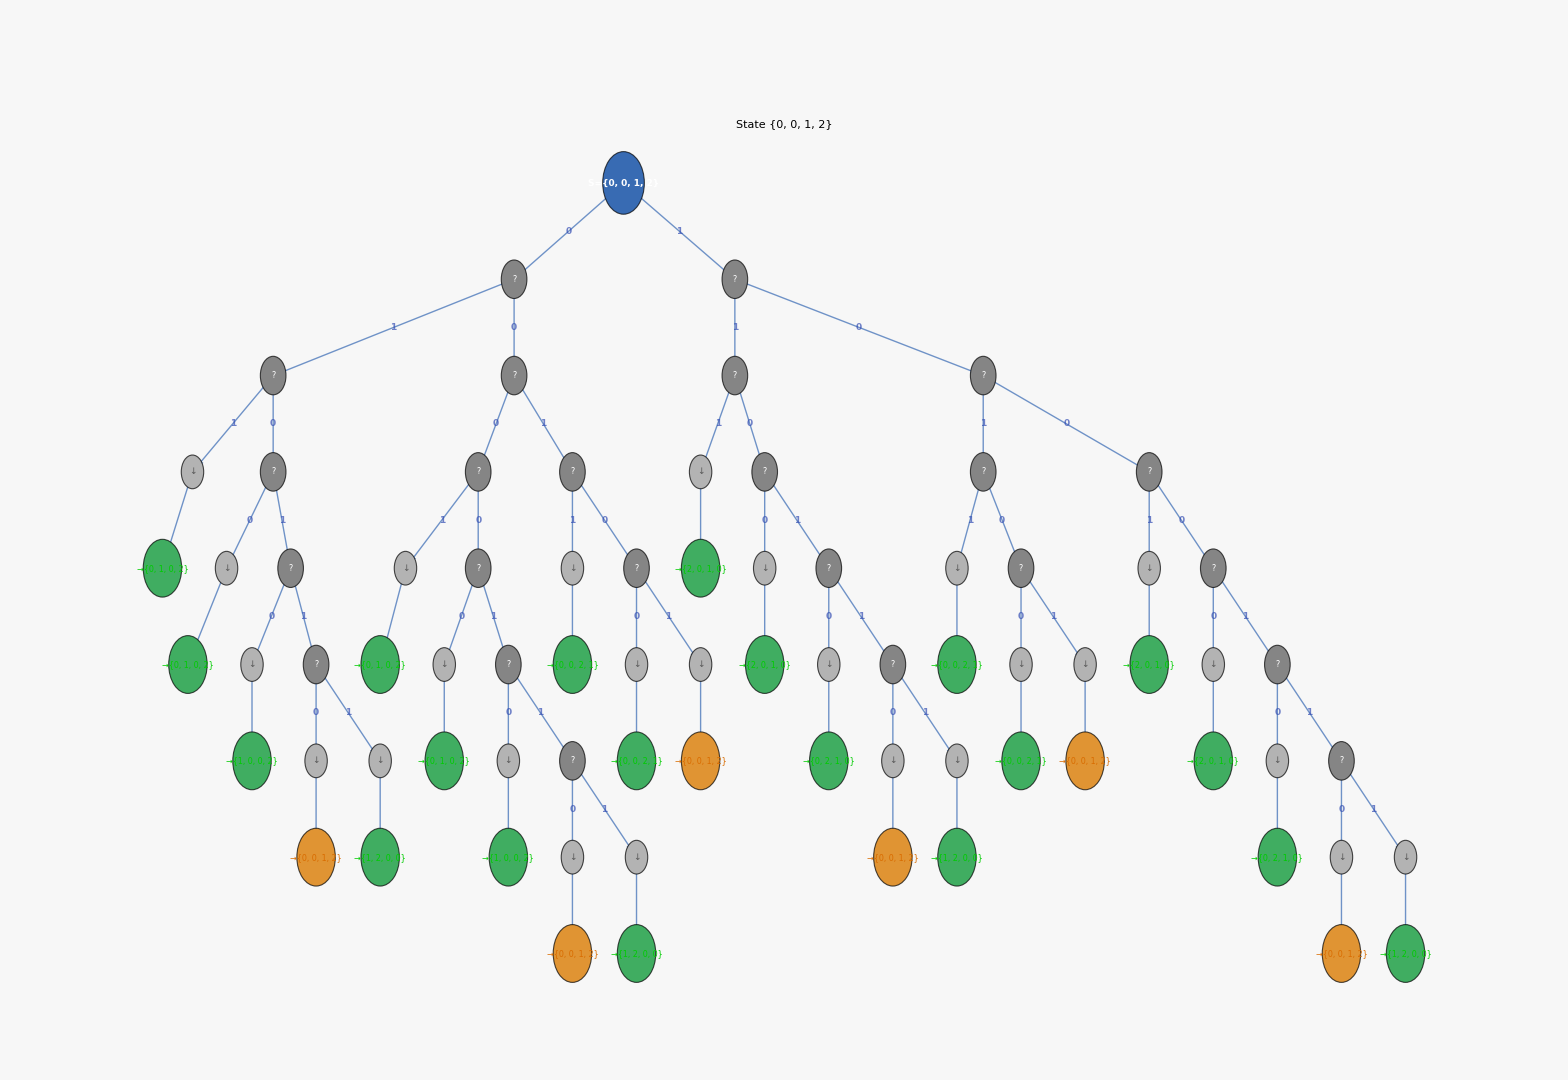
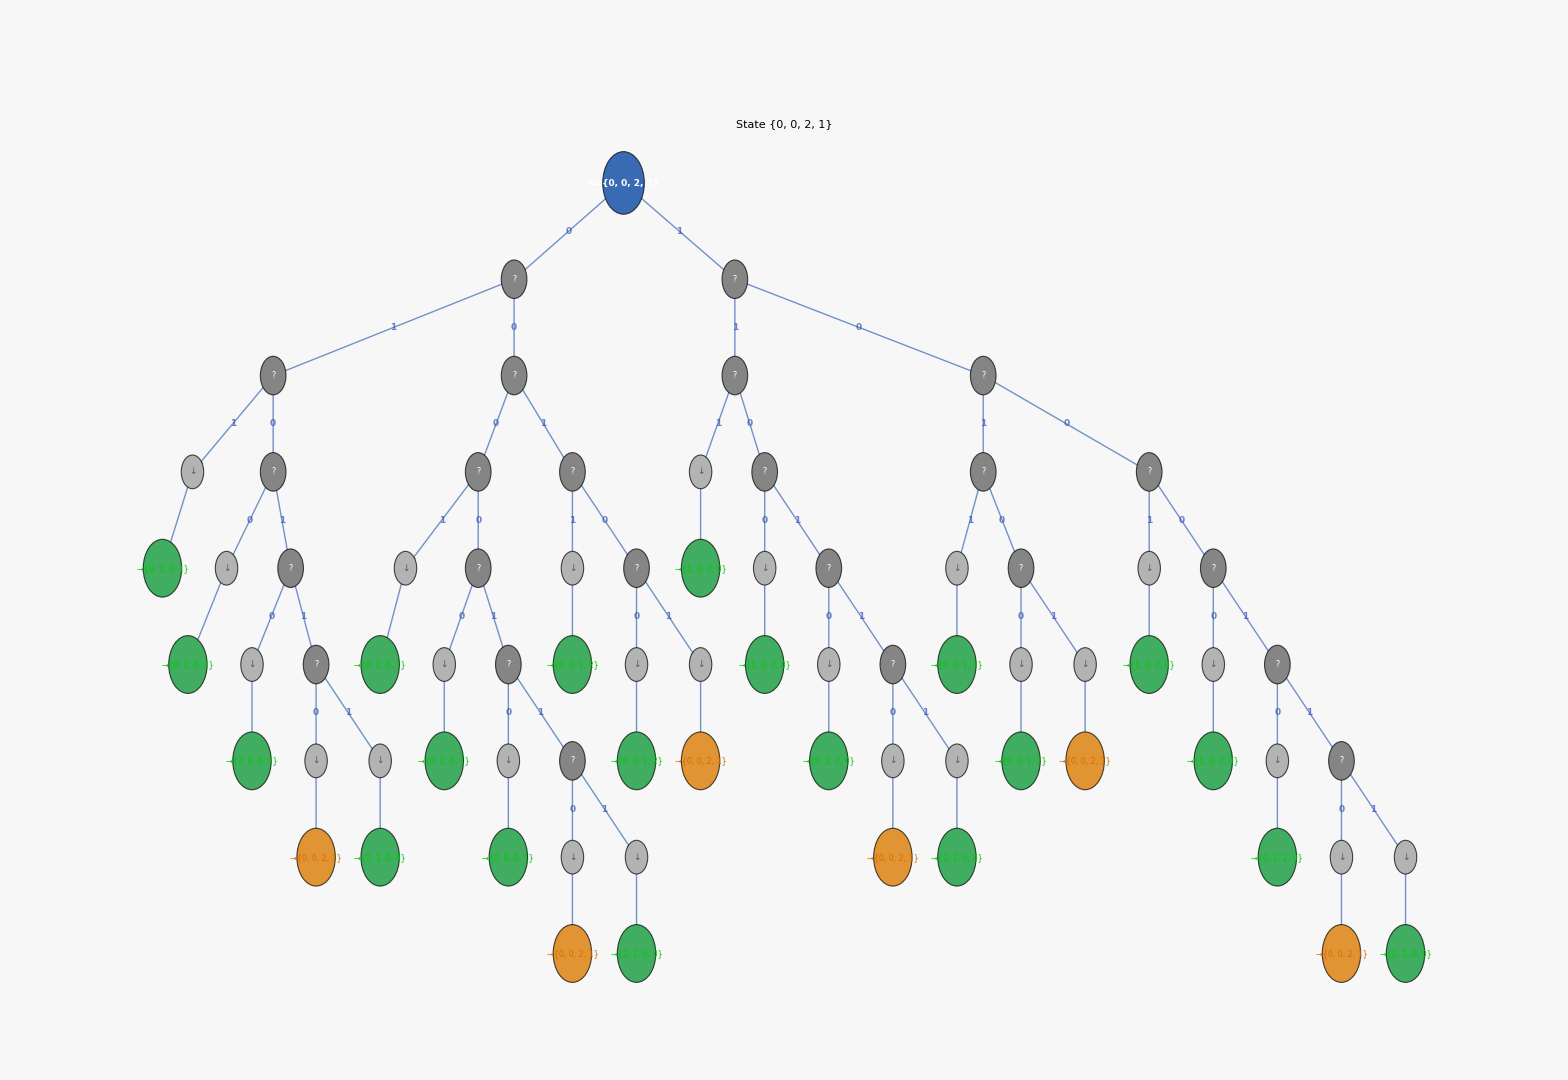
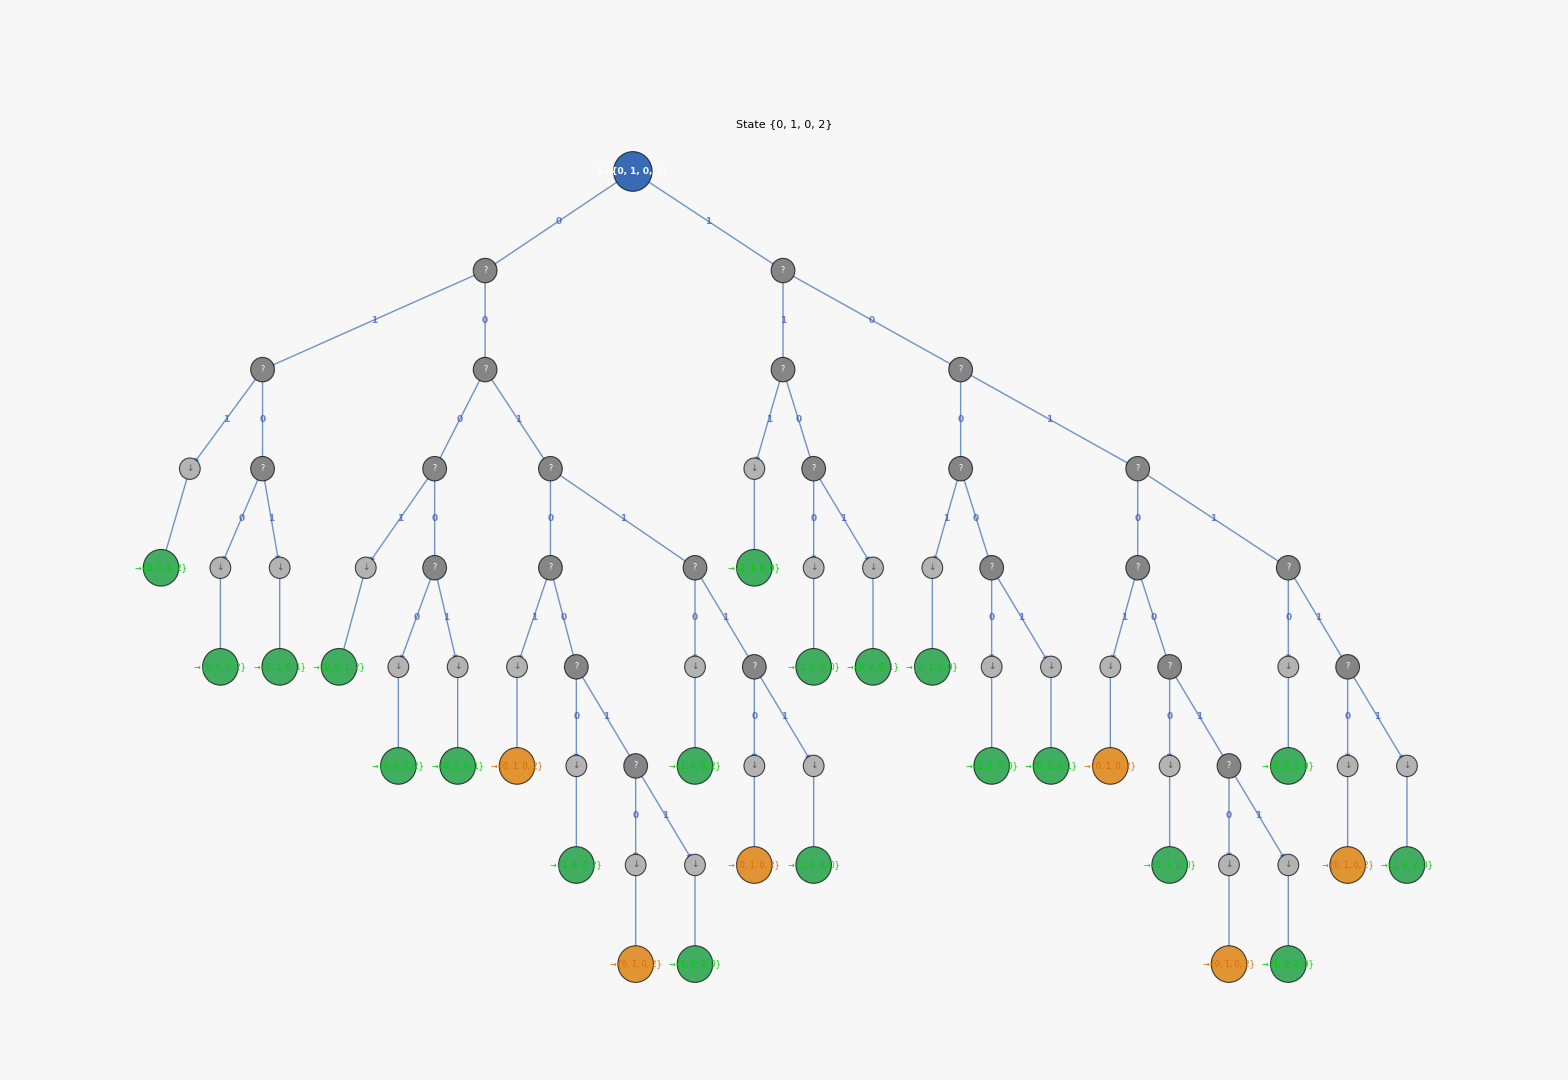
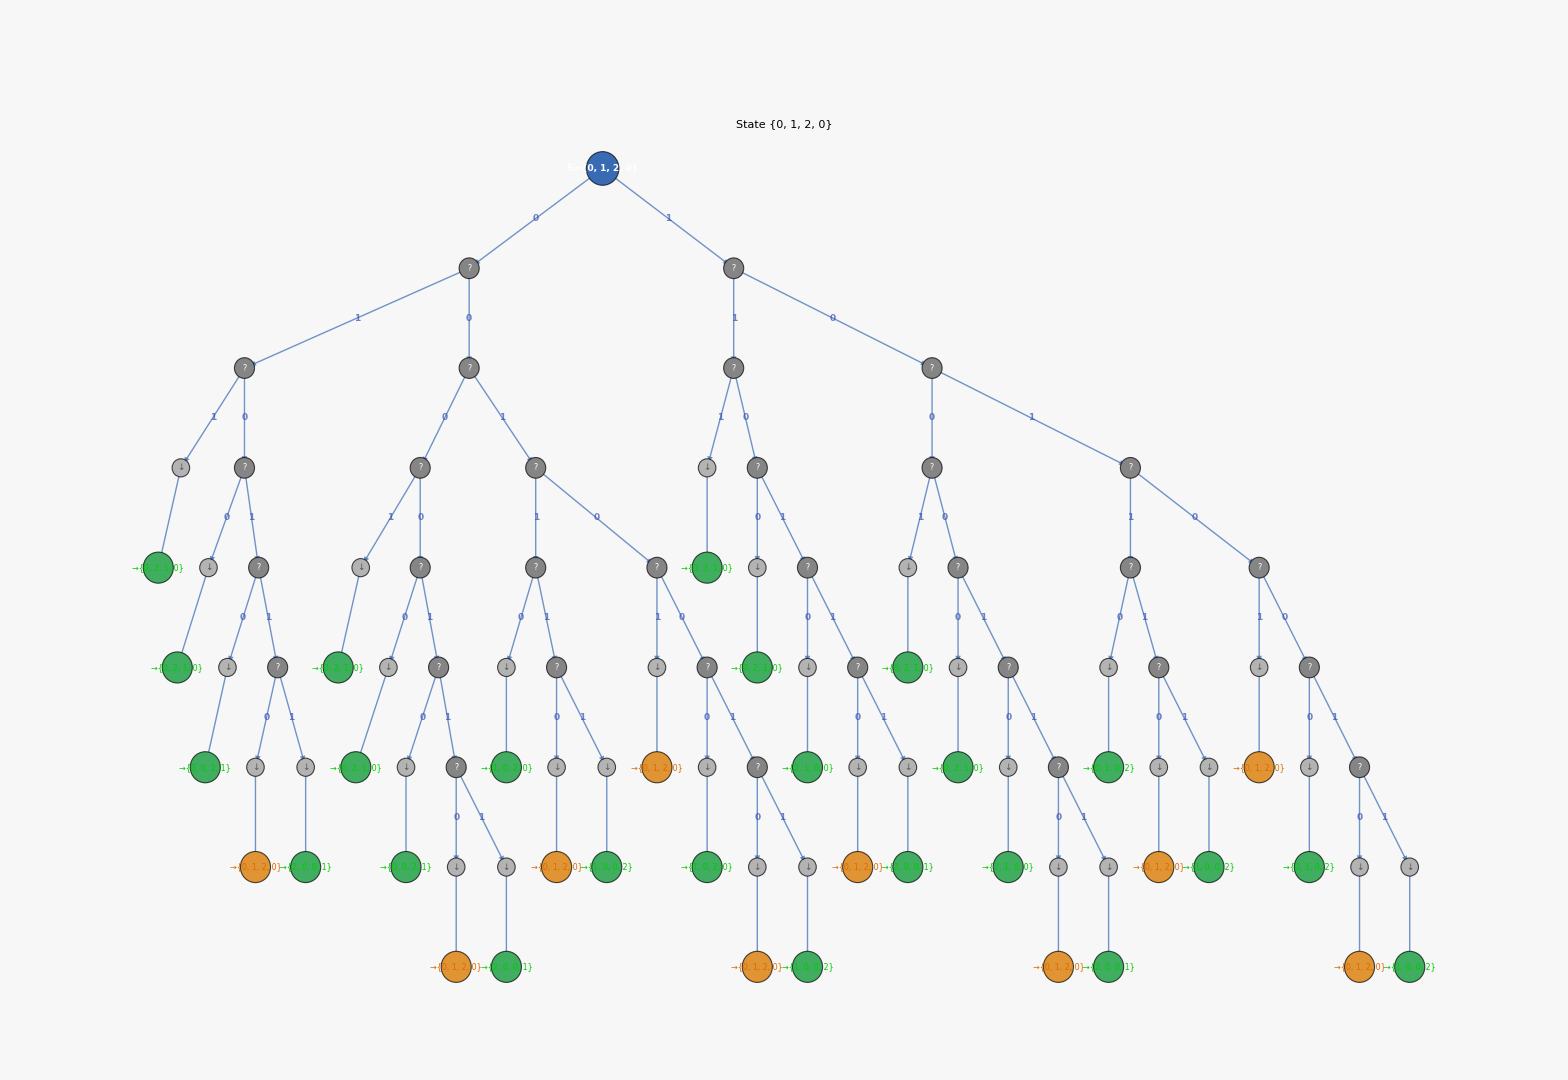
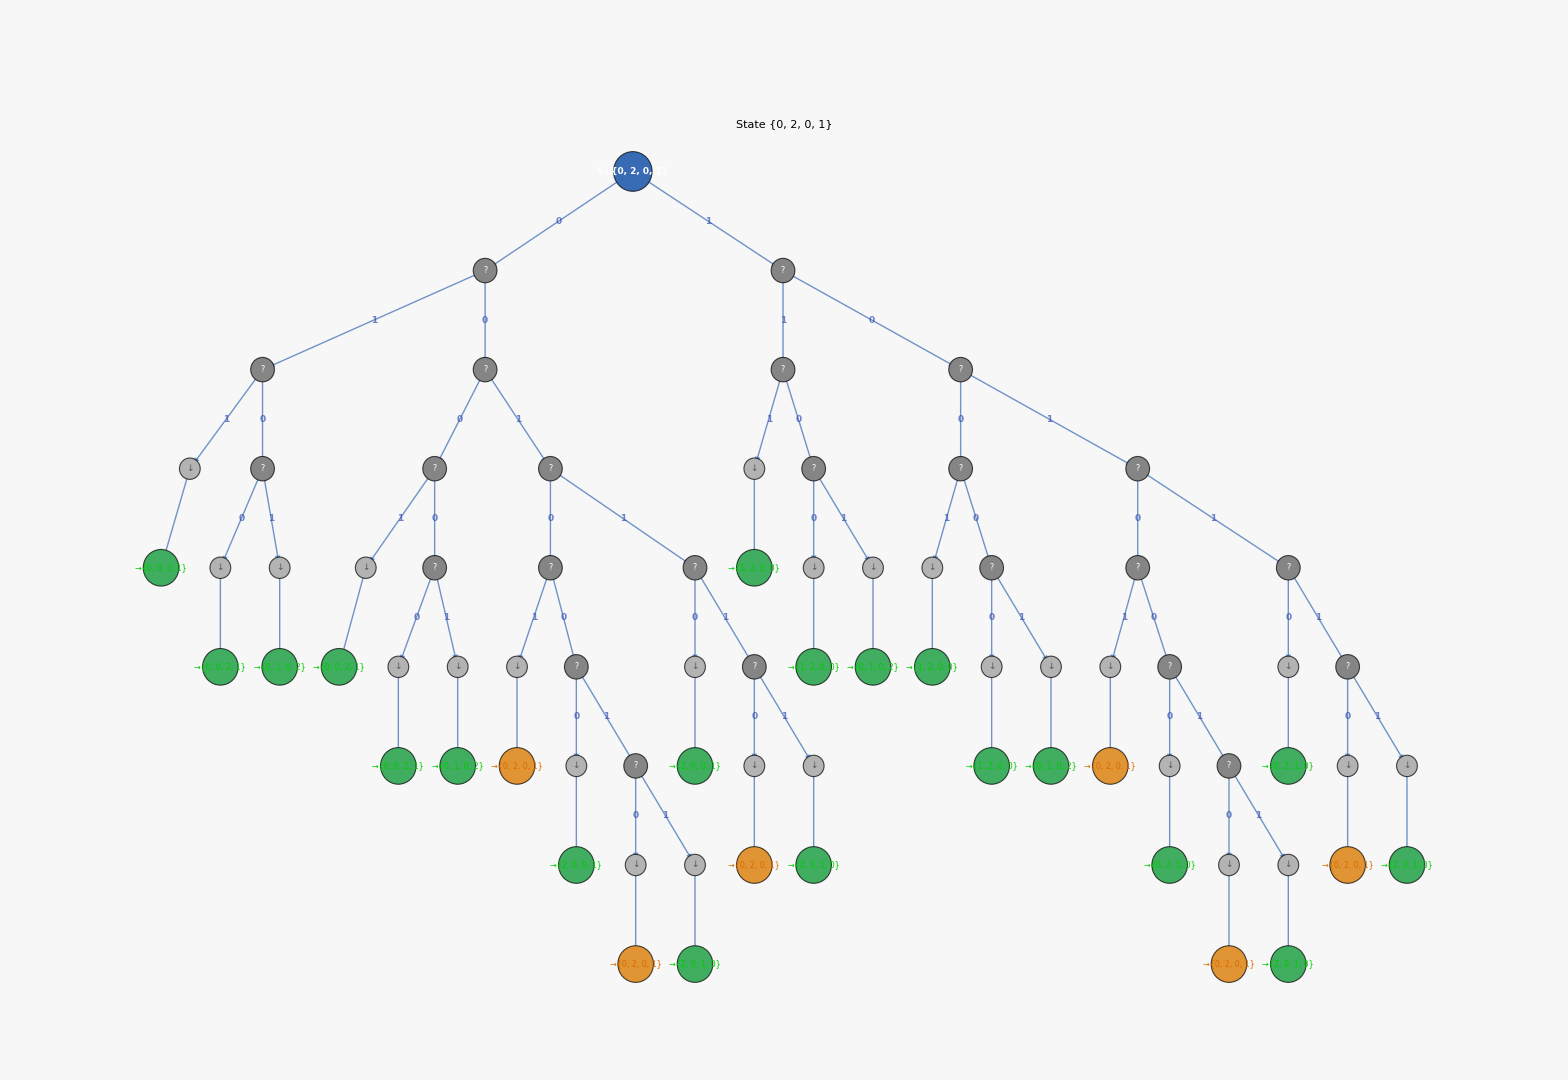
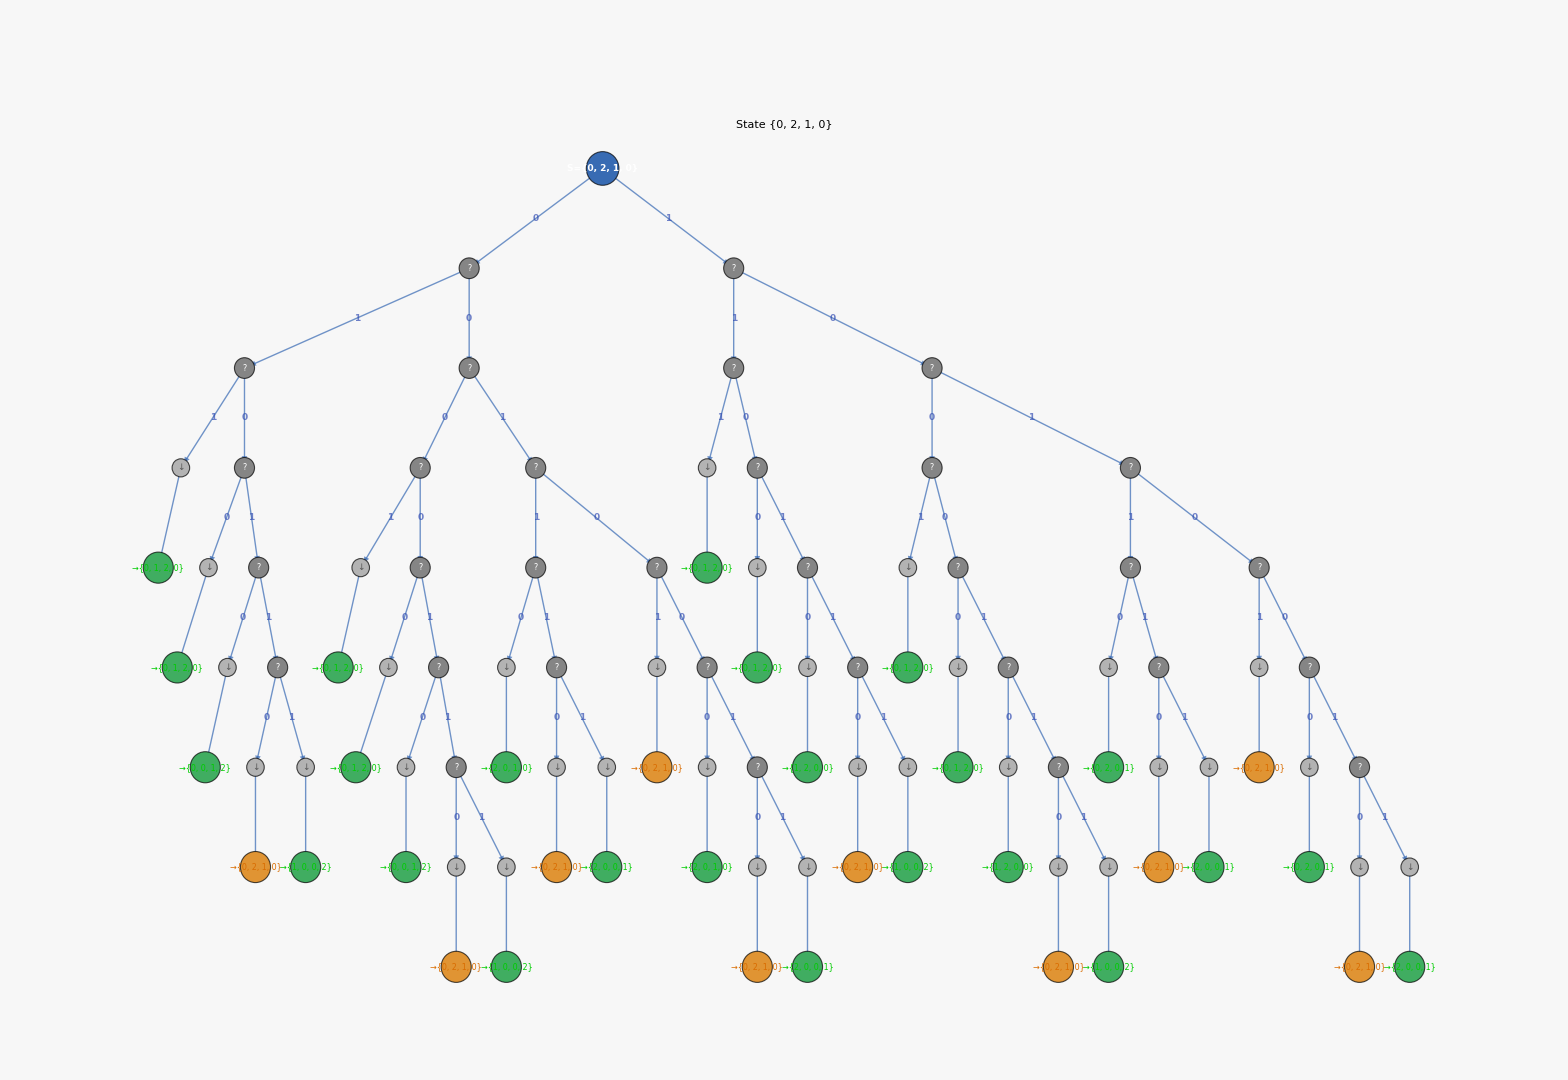
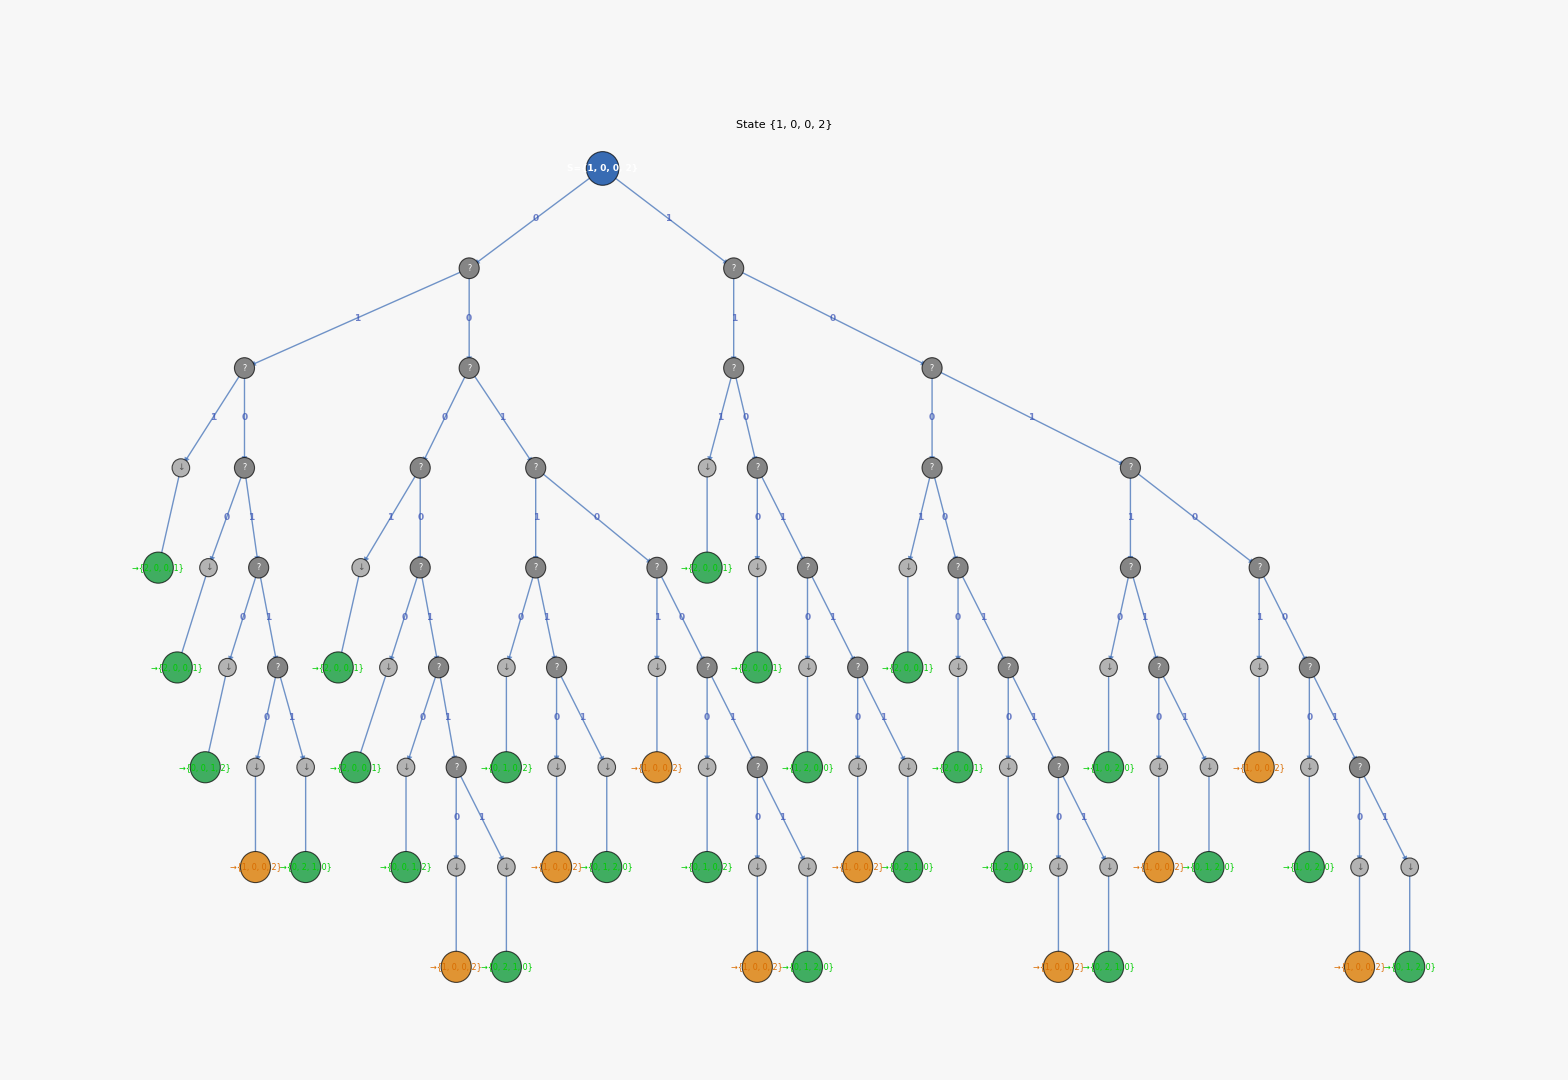
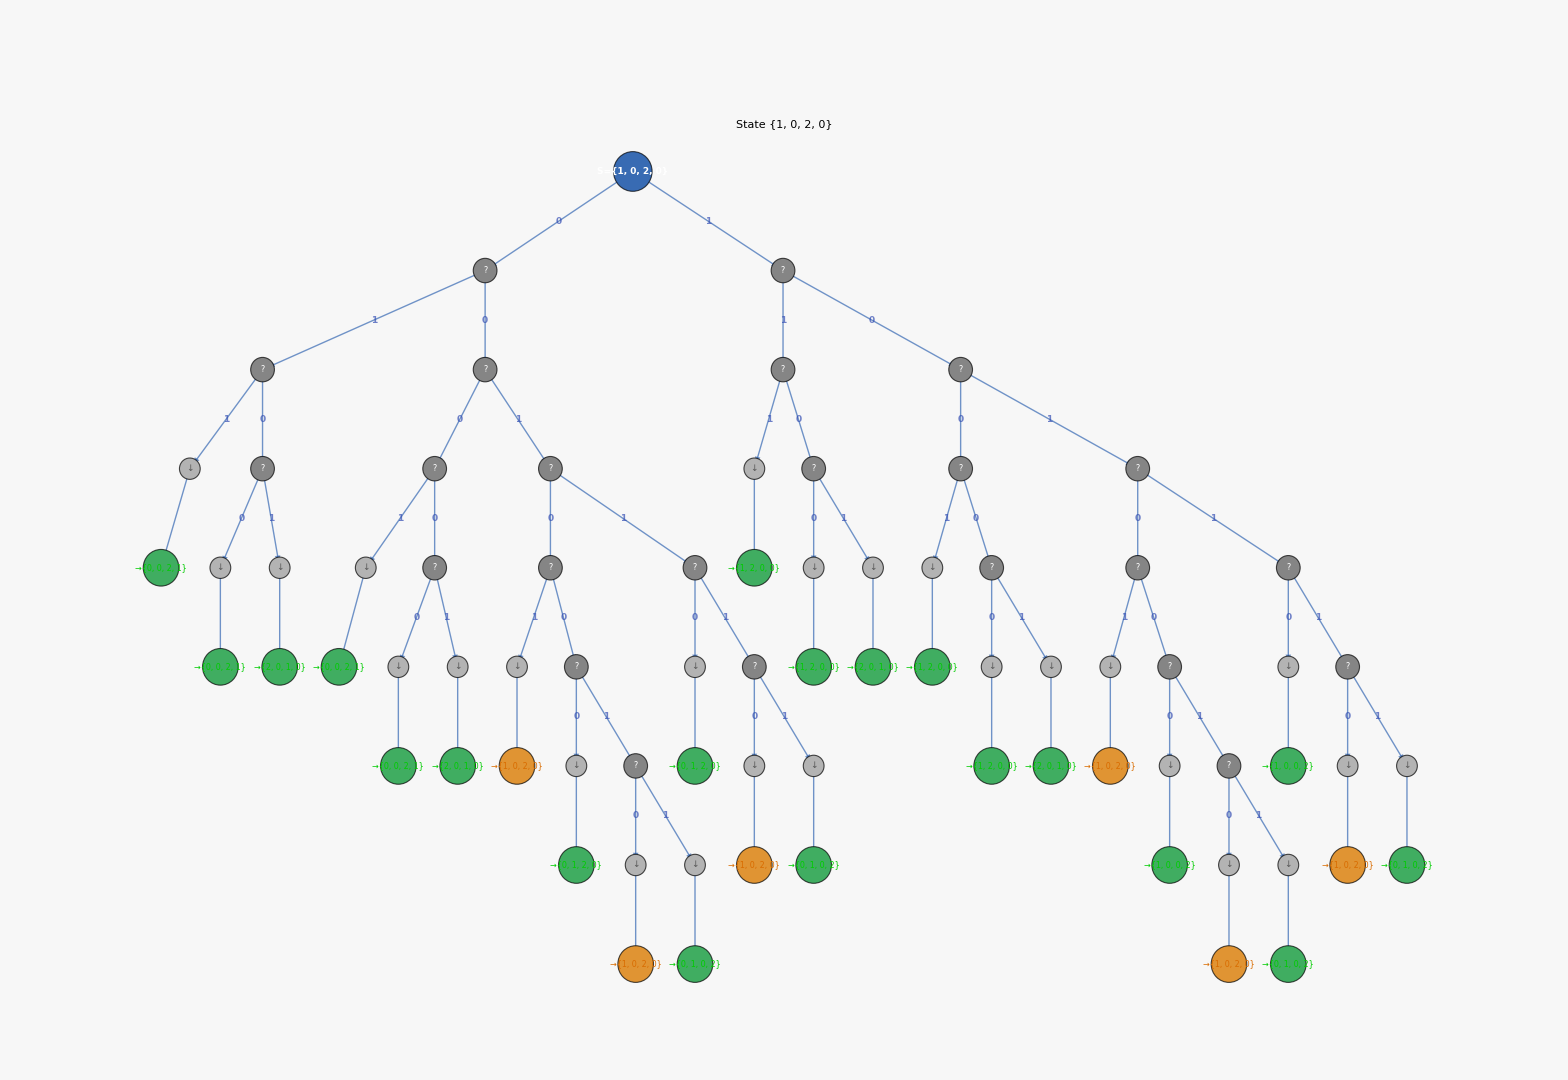
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## Symbolic Transition Matrix T[ i → j ]

Entry (i, j) = total probability of transitioning FROM state i TO state j, accumulated over all execution paths.  β is kept symbolic throughout.

T[i→j] | {0, 0, 1, 2} | {0, 0, 2, 1} | {0, 1, 0, 2} | {0, 1, 2, 0} | {0, 2, 0, 1} | {0, 2, 1, 0} | {1, 0, 0, 2} | {1, 0, 2, 0} | {1, 2, 0, 0} | {2, 0, 0, 1} | {2, 0, 1, 0} | {2, 1, 0, 0}
{0, 0, 1, 2} | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0
{0, 0, 2, 1} | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}]
{0, 1, 0, 2} | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | 0 | 0 | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2)
{0, 1, 2, 0} | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2)
{0, 2, 0, 1} | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | 0 | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | 0
{0, 2, 1, 0} | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0
{1, 0, 0, 2} | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | 0 | 0
{1, 0, 2, 0} | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | 0
{1, 2, 0, 0} | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | 0 | 0 | 0 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | 0 | 0 | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2
{2, 0, 0, 1} | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | 0 | 0 | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,2)-couplingJ(1,2,1))), couplingJ(1,2,1)>couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2)
{2, 0, 1, 0} | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | 0 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2)
{2, 1, 0, 0} | 0 | Piecewise[{{(erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) (ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2)))-1))/(erf(3/(2 √2 sigStep)))^2, couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}] | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | 0 | 0 | 0 | 0 | (erf(1/(2 √2 sigStep)) (erf(3/(2 √2 sigStep))-erf(1/(2 √2 sigStep))))/(erf(3/(2 √2 sigStep)))^2 | (erf(1/(2 √2 sigStep)) (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep))) ((Piecewise[{{1-ⅇ^(β (couplingJ(1,2,1)-couplingJ(1,2,2))), couplingJ(1,2,1)<couplingJ(1,2,2)}, {0, True}}])-1))/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep))-erf(3/(2 √2 sigStep)))^2/(2 (erf(3/(2 √2 sigStep)))^2) | (erf(1/(2 √2 sigStep)))^2/(erf(3/(2 √2 sigStep)))^2

## Detailed Balance Check: T(i→j)·π(i) = T(j→i)·π(j)

Every pair of distinct states is tested using FullSimplify with β > 0.  π(s) = Exp[−β E(s)].

State i | State j | T(i→j)·π(i)  −  T(j→i)·π(j) | Result
{0, 0, 1, 2} | {0, 0, 2, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {0, 1, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {0, 1, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {0, 2, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {0, 2, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {1, 0, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 1, 2} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {0, 1, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {0, 1, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {0, 2, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {0, 2, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {1, 0, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 0, 2, 1} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {0, 1, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {0, 2, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {0, 2, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {1, 0, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 0, 2} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {0, 2, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {0, 2, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {1, 0, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 1, 2, 0} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {0, 2, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {1, 0, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 0, 1} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 1, 0} | {1, 0, 0, 2} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 1, 0} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 1, 0} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 1, 0} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 1, 0} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{0, 2, 1, 0} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 0, 2} | {1, 0, 2, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 0, 2} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 0, 2} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 0, 2} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 0, 2} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 2, 0} | {1, 2, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 2, 0} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 2, 0} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 0, 2, 0} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 2, 0, 0} | {2, 0, 0, 1} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 2, 0, 0} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{1, 2, 0, 0} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{2, 0, 0, 1} | {2, 0, 1, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{2, 0, 0, 1} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS
{2, 0, 1, 0} | {2, 1, 0, 0} | = 0   (FullSimplify, β > 0) | ✓ PASS

## Numerical MCMC Validation

The algorithm is run as a live Markov chain with genuinely random bits.  Simulated state frequencies are compared to the analytical Boltzmann distribution Exp[−βE(s)] / Z.

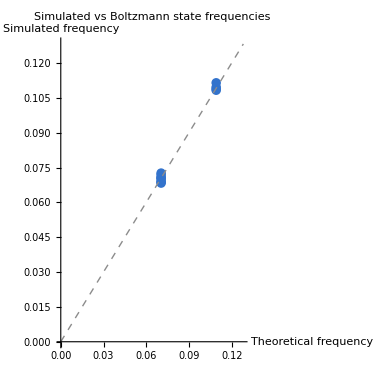
-Graphics-

Pearson r = 0.9973     KL = 0.0001     ✓ Consistent with Boltzmann